## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

Get::noopen: Cannot open pyramidalCyclope1DOverConstrained`.

Get::noopen: Cannot open pyramidalCyclope1DConstrainedNewMethod`.

```mathematica
noteBookMode="ConstrainedCorrelation";
```

## Test Points {line1, line2, pyrf12}

```mathematica
dis=1;
```

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1+RandomReal[{-0.05,0.05}],0+RandomReal[{-0.05,0.05}]],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1+RandomReal[{-0.05,0.05}],0+RandomReal[{-0.05,0.05}]],{p,1-dis,30-dis}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30}];
```

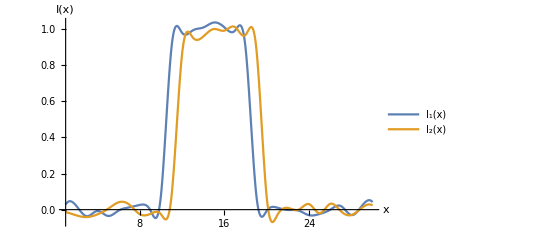

```mathematica
g0=Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30},PlotLegends->{Style["I_1(x)",FontSize->fontsize,FontFamily->"Times",Italic],Style["I_2(x)",FontSize->fontsize,FontFamily->"Times",Italic]},AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times",Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times",Italic]}];

convInitial=g0
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-initial.pdf"}],convInitial]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\pyramidalConvergenceMap2-noise-initial.pdf

## Functions

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

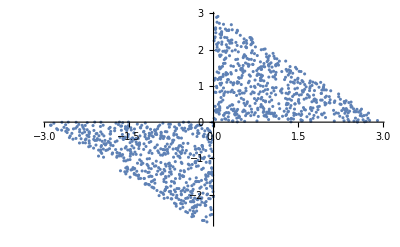

```mathematica
(* Creating list of initial Values *)
range={-3,3};
listv0=Select[RandomReal[range,{5000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
ListPlot[listv0]
```

## Map Convergence

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && 0<(*Abs[*)Total[x[[1;;2]]](*]*)<dis+1;
```

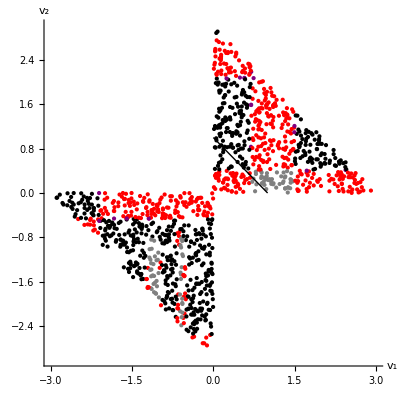
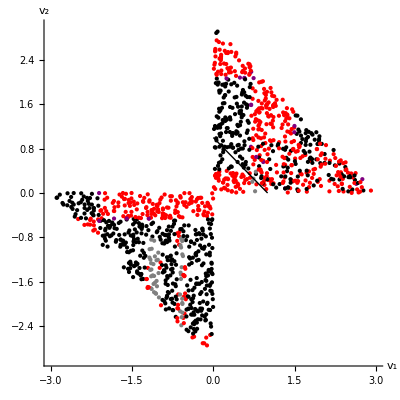
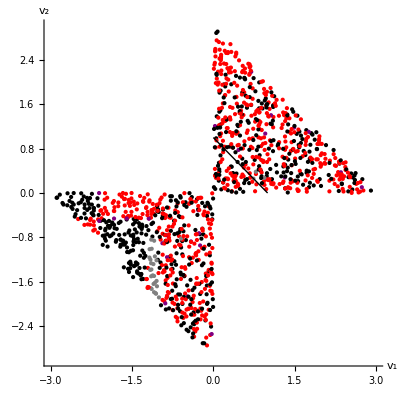
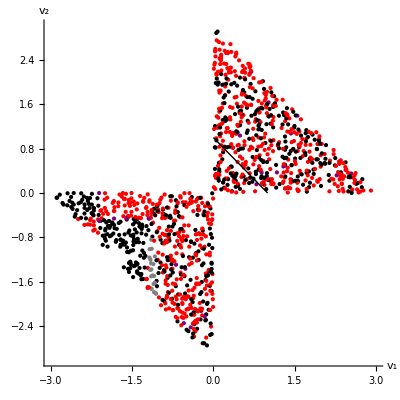
{-Graphics-Levels {1,1},-Graphics-Levels {1,2},-Graphics-Levels {1,3},-Graphics-Levels {1,4}}

```mathematica
lvlmin=1;
lvlmax=4;
p=13;
dis=dis;

g0Table=Table[
Labeled[pixelInitialValueGraphics[10,0,0,p,listv0,condition,dis, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),noteBookMode],Style[Row[{"Levels {",lvlmin,",",lvlmax,"}"}],FontSize->30,FontFamily->"Times",Italic],Top]

,{lvlmax,Range[1,4]}]
```

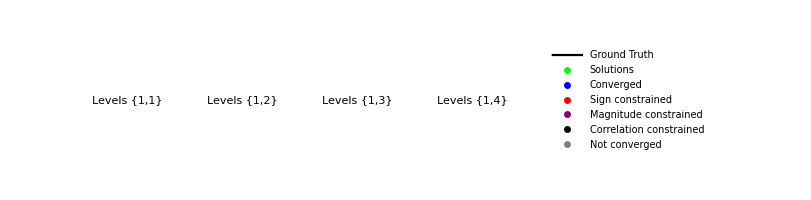

```mathematica
g0final=Legended[GraphicsRow[g0Table, ImageSize->{600,200}],{LineLegend[{Black},{Style["Ground Truth",FontSize->25]}],PointLegend[{Green,Blue,Red,Purple,Black,Gray},Style[#, FontSize->25]&/@{"Solutions","Converged","Sign constrained","Magnitude constrained","Correlation constrained","Not converged"}]}]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-map.pdf"}],g0final,ImageSize->1600]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\pyramidalConvergenceMap2-noise-map.pdf

## A few points

```mathematica
g0Table=Table[
Labeled[pixelInitialValueGraphics[10,0,0,p,listv0,condition,dis, pyrf12[[1;;4]],0.001*2^(-lvlmin+1),noteBookMode],Style[Row[{"Convergence for p= ",p}],FontSize->30,FontFamily->"Times",Italic],Top]

,{p,Range[1,30,3]}];
```

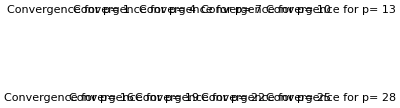

```mathematica
g0TableFinal=Legended[GraphicsGrid[Partition[g0Table,5]],{LineLegend[{Black},{Style["Ground Truth",FontSize->30]}],PointLegend[{Green,Blue,Red,Purple,Black,Gray},Style[#, FontSize->30]&/@{"Solutions","Converged","Sign constrained","Magnitude constrained","Correlation constrained","Not converged"}]}]
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-all.pdf"}],g0TableFinal,ImageSize->1900]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\pyramidalConvergenceMap2-noise-all.pdf

## Graphical solutions

```mathematica
lvlmax=4;
```

```mathematica
(* This function is called from pyramidalCyclope1D *)
range={{0,0}};
g1=Labeled[seeAllLine[0,0,range,condition,Range[p-1,p+1],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"[a,b]= [",range[[1,1]],",",range[[1,2]],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top];
```

```mathematica
(* This function is called from pyramidalCyclope1D *)
range={{0.7,0.2}};
gc=Labeled[seeAllLine[0,0,range,condition,Range[p-1,p+1],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"[a,b]= [",range[[1,1]],",",range[[1,2]],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top];
```

```mathematica
(* This function is called from pyramidalCyclope1D *)
range={{0.2,0.6}};

g2=Labeled[seeAllLine[0,0,range,condition,Range[p-1,p+1],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"[a,b]= [",range[[1,1]],",",range[[1,2]],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top];
```

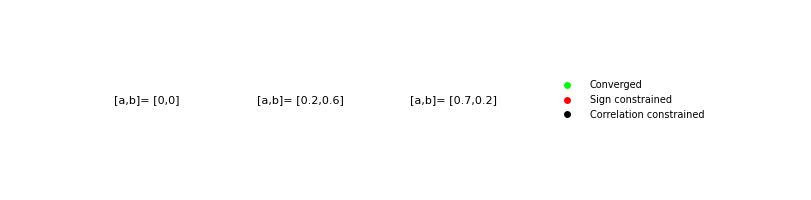
-Graphics-Convergence when v_0∈[a,b] for p=11

```mathematica
convFinal=Labeled[Legended[GraphicsRow[{g1,g2,gc},ImageSize->{600,200},Spacings->{-220,-150}],{(*Placed[LineLegend[{LightBlue,LightOrange},{Style["i_a",FontSize->fontsize,FontFamily->"Times",Italic],Style["i_b",FontSize->fontsize,FontFamily->"Times",Italic]}],Below],*)Placed[PointLegend[{Green,Red,Black},{"Converged","Sign constrained","Correlation constrained"}],Right]}],Row[{Style[Row[{"Convergence when "}],FontSize->fontsize,FontFamily->"Times"],Style[Row[{"v_0∈[a,b] "}],FontSize->fontsize,FontFamily->"Times",Italic],Style[Row[{"for "}],FontSize->fontsize,FontFamily->"Times"],Style[Row[{"p=11"}],FontSize->fontsize,FontFamily->"Times",Italic]}],Top]
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-convergence.pdf"}],convFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\pyramidalConvergenceMap2-noise-convergence.pdf

```mathematica
giter=Partition[pixelIterGraphics[10,0,0, p,{{0,0}},condition,2, lvlmax-1,pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],10][[All,-1]];
```

```mathematica
giter
```

{}

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-iterations.pdf"}],giter, ImageSize->Large]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\pyramidalConvergenceMap2-noise-iterations.pdf

## Graphical solutions

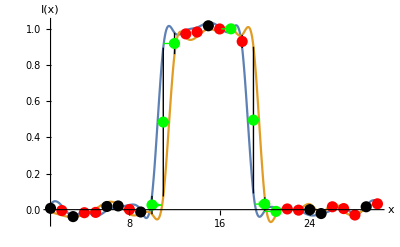
-Graphics-v_o∈[-3,3]

```mathematica
(* This function is called from pyramidalCyclope1D *)
range=listv0;
g1=Labeled[seeAllLine[0,0,range,condition,Range[1,30],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"v_o∈[-3,3]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top]
```

## Test Points {line1, line2, pyrf12}

```mathematica
dis=1;
```

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-dis,30-dis}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,4];
pyrf2=pyrFuncGen[line2,4];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30}];
```

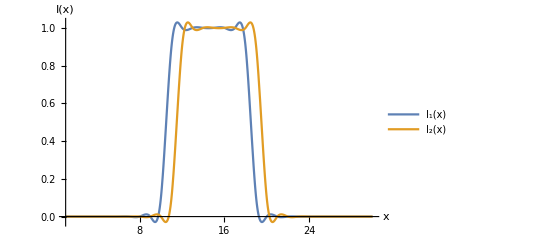

```mathematica
g0=Plot[{pyrf12[[1,1,1]][x],pyrf12[[1,2,1]][x]},{x,1,30},PlotLegends->{Style["I_1(x)",FontSize->fontsize,FontFamily->"Times",Italic],Style["I_2(x)",FontSize->fontsize,FontFamily->"Times",Italic]},AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times",Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times",Italic]}];

convInitial=g0
```

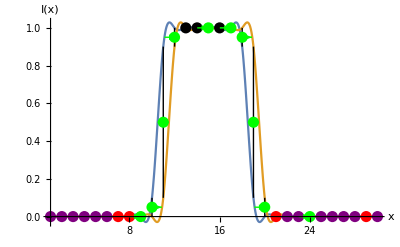
-Graphics-v_o∈[-3,3]

```mathematica
(* This function is called from pyramidalCyclope1D *)
range=listv0;
g2=Labeled[seeAllLine[0,0,range,condition,Range[1,30],pyrf12[[lvlmin;;lvlmax]],0.001,noteBookMode],Style[Row[{"v_o∈[-3,3]"}],FontSize->fontsize,FontFamily->"Times",Italic],Top]
```

```mathematica
g3=GraphicsRow[{g2,g1},Spacings->{-450,-100},ImageSize->{500,200}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-All2.pdf"}],g3, ImageSize->{900,500}]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\pyramidalConvergenceMap2-noise-All2.pdf

## Test Points {line1, line2, pyrf12}

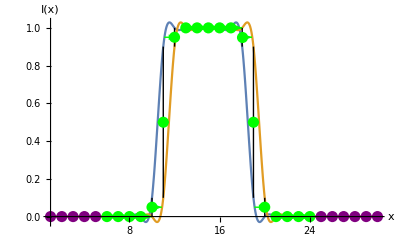
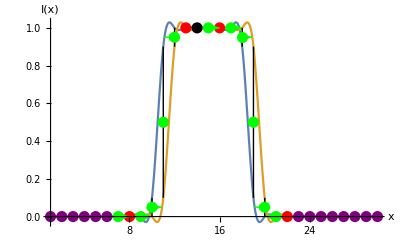
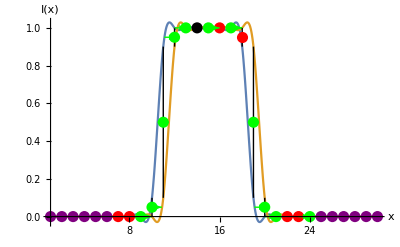
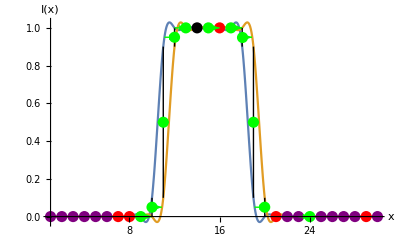
{-Graphics-Pyramidal constraint n= 0,-Graphics-Pyramidal constraint n= 1,-Graphics-Pyramidal constraint n= 2,-Graphics-Pyramidal constraint n= 3}

```mathematica
(* This function is called from pyramidalCyclope1D *)
(* Creating list of initial Values *)
range={-3,3};
listv0=Select[RandomReal[range,{2500,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
ListPlot[listv0];

gTable=Table[
Labeled[seeAllLine[0,0,listv0,condition,Range[1,30],pyrf12[[lvlmin;;n+1]],0.001,noteBookMode],Style[Row[{"Pyramidal constraint n= ", n}],FontSize->fontsize,FontFamily->"Times",Italic],Top]
,{n, Range[0,3]}]
```

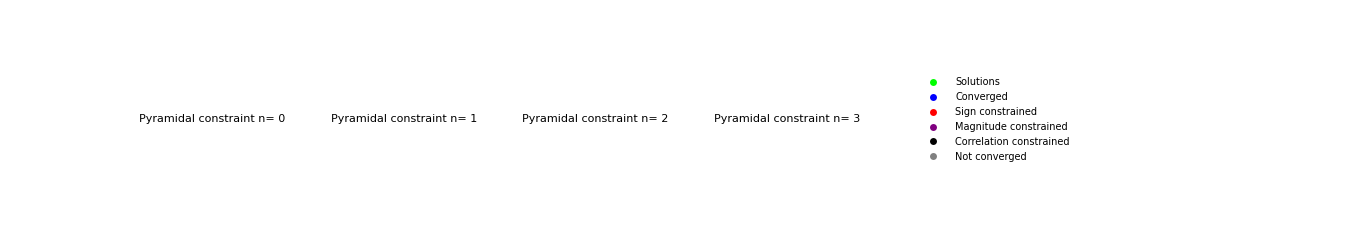

```mathematica
gTable2=Legended[GraphicsRow[gTable,Spacings->{-400, -100},ImageSize->1000],{PointLegend[{Green,Blue,Red,Purple,Black,Gray},Style[#, FontSize->20]&/@{"Solutions","Converged","Sign constrained","Magnitude constrained","Correlation constrained","Not converged"}]}]
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-AllNlvl.pdf"}],gTable2,ImageSize->1000]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\pyramidalConvergenceMap2-noise-AllNlvl.pdf